links útiles
	- https://mathematica.stackexchange.com/questions/111555/solving-simple-transcendental-equation

```mathematica
V0=5.0
a=2.0
```

5.

2.

Resolvemos de forma numérica la ecuación trascendente de la energía para las autofunciones pares.

```mathematica
Reduce[{Tan[a*Sqrt[2x]]^2==V0/x-1,0<x<V0},x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x==0.229468||x==0.437648||x==2.02304||x==4.39045||x==4.99315

Entonces las energías serán:

```mathematica
e1=-(V0-0.22946761941103294)
e2=-(V0-0.43764836962050485)
e3=-(V0-2.0230376377914085)
e4=-(V0-4.390445186244791)
e5=-(V0-4.993145731389166)
```

-4.77053

-4.56235

-2.97696

-0.609555

-0.00685427

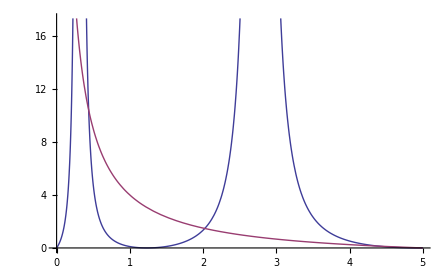

```mathematica
Plot[{Tan[a*Sqrt[2x]]^2,V0/x-1},{x,0,V0}]
```

Resolvemos de forma numérica la ecuación trascendente de la energía para las autofunciones impares.

```mathematica
Reduce[{Cot[a*Sqrt[2x]]^2==V0/x-1,0<x<V0},x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::incs: Warning: Reduce was unable to prove that the solution set found is complete.

x==0.91155||x==1.78862+0. ⅈ||x==3.50054+0. ⅈ

Entonces las energías serán:

```mathematica
e1=-(V0-0.9115501970546065)
e2=-(V0-1.7886231565731017)
e3=-(V0-3.500540070843472)
```

-4.08845

-3.21138

-1.49946

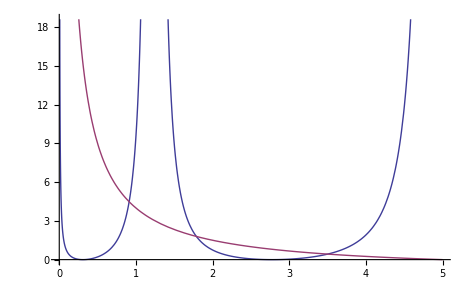

```mathematica
Plot[{Cot[a*Sqrt[2x]]^2,V0/x-1},{x,0,V0}]
```